# γγ Scattering

## Notation, η, etc.

```mathematica
(* Define notation to be used throughout this notebook*)
<<Notation`
Notation[Subscript[g_, x_,y_] ⟺ g_[[x_,y_]]]
Notation[g_^(x_,y_) ⟺ Inverse[g_][[x_,y_]]]
Notation[Subscript[x_, μ_] ⟺ Lower[x_][[μ_]]]
Notation[Subscript[F_, a_,b_](k_,n_,λ_) ⟺ F_[k_,n_,λ_][[a_,b_]]];
```

```mathematica
g=1/z^2{{1,0,0,0,0},{0,0,-1/2,0,0},{0,-1/2,0,0,0},{0,0,0,1,0},{0,0,0,0,1}};
η={{0,-1/2,0,0},{-1/2,0,0,0},{0,0,1,0},{0,0,0,1}};
X={pl,mn,pp1,pp2};
sProd[x_,y_]:=sProd[x,y]=Simplify[∑_(μ=1)^4 ∑_(ν=1)^4 x[[μ]] y[[ν]] Subscript[η, μ,ν]];
Lower[y_]:=Lower[y]=Table[∑_(j=1)^4 Subscript[η, i,j] y⟦j⟧,{i,1,4}];
```

## Kinematics

```mathematica
(* Kinematics of the incoming photons*)
```

```mathematica
k1={√s,-Q1^2/(√s),0,0};k2={-Q2^2/(√s),√s,0,0};
n1={{0,0,1,0},{0,0,0,1},1/Q1{√s,Q1^2/(√s),0,0}};
n2={{0,0,1,0},{0,0,0,1},1/Q2{Q2^2/(√s),√s,0,0}};
```

```mathematica
(* Kinematics of the outgoing photons*)
k3γ=-{√s,(qx^2+qy^2-Q3^2)/(√s),qx,qy};k4γ=-{(qx^2+qy^2-Q4^2)/(√s),√s,-qx,-qy};
n3γ={{0,2 qx/(√s),1,0},{0,2 qy/(√s),0,1},1/Q3{√s,(Q3^2+qx^2+qy^2)/(√s),qx,qy}};
n4γ={{-2 qx/(√s),0,1,0},{-2 qy/(√s),0,0,1},1/Q4{(Q4^2+qx^2+qy^2)/(√s),√s,-qx,-qy}};
```

```mathematica
(* Kinematics of the outgoing meson *)
k3Meson=-{√s,(qx^2+qy^2+m3^2)/(√s),qx,qy};k4Meson=-{(qx^2+qy^2+m4^2)/(√s),√s,-qx,-qy};
n3Meson={{0,2 qx/(√s),1,0},{0,2 qy/(√s),0,1},1/m3{√s,(-m3^2+qx^2+qy^2)/(√s),qx,qy}};
n4Meson={{2 qx/(√s),0,1,0},{2 qy/(√s),0,0,1},1/m4{(-m4^2+qx^2+qy^2)/(√s),√s,qx,qy}};
```

## AdS States

Defining AdS

```mathematica
Unprotect@Print;
Print = Null;
<<xAct`xPert`;
<<xAct`xPand`;
<<xAct`SplitExpression`.1d ;
(* Define a 5d manifold M *)
DefManifold[M,5,{a,b,c,d,m,n}];
(* We also define a metric on this manifold,with negative determinant and associated covariant derivative CD.This derivative is extended to act on tensor densities defined using the determinant of the metric g in the basis AIndex: *)
DefMetric[-1,g[-m,-n],CD,{";","∇"},WeightedWithBasis->AIndex];
DefParameter[z];
(* Use the same notation as Alfonso *)
$CovDFormat="Prefix";
(* Because we shall work with a single covariant derivative operator,we can choose a simpler output for the geometric tensors *)
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
(* Definition of the warp factor A. Later we set it as -Log[z]*)
DefTensor[A[],M,PrintAs->"A"];
(* Define the U(1) gauge field *)
DefTensor[V[-a],M,PrintAs->"V"];
DefTensor[Vz[],M,PrintAs->"V_z"];
(* colour in blue the perturbative orders *)
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
(* splitting code *)
DefManifold[flat,4,{μ,ν,λ,ρ,σ,α,β}];
DefMetric[-1,η[-μ,-ν],CDflat,{"|","𝒟"}];
DefTensor[Vflat[-μ],flat,PrintAs->"V"];
η/:PD[_][η[__]]:=0;
A/:PD[_][A[]]:=0;
DefSplitting[AAdS,M->{z,flat}];
SplittingRules[AAdS,
{g[-z,-z]->Exp[2A[]],
g[-z,-μ]->0,
g[-μ,-z]->0,
g[-μ,-ν]->Exp[2A[]]η[-μ,-ν],
g[z,z]->Exp[-2A[]],
g[z,μ]->0,
g[μ,z]->0,
g[μ,ν]->Exp[-2A[]]η[μ,ν],
V[-z]->Vz[],
V[-μ]->Vflat[-μ]
}
];
AddTensorDependencies[{g,A,V,Vz,Vflat},{z}];
(* Define metric perturbation *)
DefMetricPerturbation[g,δg,ϵ];
DefTensorPerturbation[δV[LI[order],-a],V[-a],M];
time=ComputeCurvatureTensors[AAdS]//Timing//First;
Unprotect[Print];
Print=.;
Protect[Print];
Print["Splitting curvature tensors computed in ", time, " seconds"]
```

Splitting curvature tensors computed in 1.78528 seconds

Computing Normalizable modes

```mathematica
(* Definition of Subscript[F, ab]*)
F[a_?AIndexQ,b_?AIndexQ]:=CD[a][V[b]]-CD[b][V[a]];
```

```mathematica
(*U(1) gauge field lagrangian*)
ℒ=-1/4 √(-Detg[])F[-a,-b]F[a,b];
```

```mathematica
(* Use variational method to get the EOMs *)
ExpandPerturbation@Perturbation@ℒ/.δg[__]->0;
1/(√(-Detg[]))VarD[δV[LI[1],m],CD][%]/.delta[Times[-1,LI[1]],LI[1]]->1//ContractMetric//Simplification;
eom=%
```

∇_a ∇^a V |  
m-∇_a ∇_m V | a

```mathematica
(*Compute the EOM componentwise*)
SplitExpression[AAdS,Fun->SeparateMetric[],ComponentsListQ->True][eom];
splittedEOM=%
```

-∇_n$4955 ∇_z V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
z→-ⅇ^(-2 A) ∂_z ∂_α V | α
 +ⅇ^(-2 A) ∂_α ∂^α V_z
-∇_n$4955 ∇_μ V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
μ→ⅇ^(-2 A) ∂_z A ∂_z V |  
μ-ⅇ^(-2 A) ∂_z ∂_μ V_z+ⅇ^(-2 A) ∂_z ∂_z V |  
μ+ⅇ^(-2 A) ∂_α ∂^α V |  
μ-ⅇ^(-2 A) ∂_α ∂_μ V | α
 -ⅇ^(-2 A) ∂_z A ∂_μ V_z

```mathematica
(*Apply the gauge conditions*)
splittedEOM/.{Vz[]->0,ParamD[z][PD[-α][Vflat[α]]]->0,PD[-α][PD[-μ][Vflat[α]]]->0}
```

-∇_n$4955 ∇_z V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
z→0
-∇_n$4955 ∇_μ V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
μ→ⅇ^(-2 A) ∂_z A ∂_z V |  
μ+ⅇ^(-2 A) ∂_z ∂_z V |  
μ+ⅇ^(-2 A) ∂_α ∂^α V |  
μ

```mathematica
(*Subscript[V, μ]=Subscript[n, μ] f[z] ⅇ^(ⅈp.x)*)
```

```mathematica
(*Find normalizable mode of U(1) gauge field *)
ClearAll[m];
fSol=DSolve[{m^2 f[x]-1/x f'[x]+f''[x]==0,f[0]==0},f,x][[1]]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{f→Function[{x},x BesselJ[1,m x] C[1]]}

```mathematica
(* We have a wall at z = zf to mimic confinement effects. If we impose the derivative to be zero at this wall we can establish a relationship between the mass of meson and the position of this wall.*)
(f'[zf]/.fSol//FullSimplify)
```

m zf BesselJ[0,m zf] C[1]

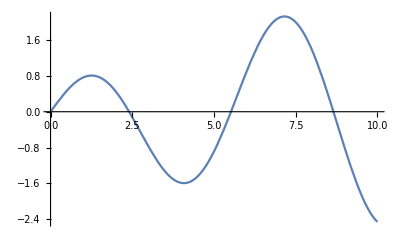

```mathematica
(* Plot the previous function to find zeros *)
Plot[x BesselJ[0,x],{x,0,10}]
```

```mathematica
FindRoot[x BesselJ[0,x],{x,2}]
```

{x→2.40483}

```mathematica
(* Given the mass m of the meson, zf = ζ / m*)
(*ζ = 2.404825557695773;*)
```

```mathematica
(*We now find C[1] through normalization of the integral 14 in the notes provided my Miguel *)
```

```mathematica
Integrate[1/z(f[z]/.fSol)^2,{z,0,zf}]//FullSimplify
(*m zf = ζ which is a root of x BesselJ[0,x]*)
%/.zf->ζ/m//Expand
%/.{ζ^2 BesselJ[0,ζ]^2->0,ζ BesselJ[0,ζ]->0}
Solve[%==1,C[1]][[2]]
```

(zf (m zf BesselJ[0,m zf]^2-2 BesselJ[0,m zf] BesselJ[1,m zf]+m zf BesselJ[1,m zf]^2) C[1]^2)/(2 m)

(ζ^2 BesselJ[0,ζ]^2 C[1]^2)/(2 m^2)-(ζ BesselJ[0,ζ] BesselJ[1,ζ] C[1]^2)/m^2+(ζ^2 BesselJ[1,ζ]^2 C[1]^2)/(2 m^2)

(ζ^2 BesselJ[1,ζ]^2 C[1]^2)/(2 m^2)

{C[1]→(√2 m)/(ζ BesselJ[1,ζ])}

```mathematica
fNAdS[z_]:=(√2 m)/(ζ BesselJ[1,ζ])z BesselJ[1,m z];
dfNAdS[z_]:=(√2 m^2)/(ζ BesselJ[1,ζ])z BesselJ[0,m z];
```

```mathematica
FNAdS[k_,n_,λ_]:=FNAdS[k,n,λ]=Exp[ⅈ sProd[k,X]]{ dfNAdS[z]{0,Subscript[n[[λ]], 1],Subscript[n[[λ]], 2],Subscript[n[[λ]], 3],Subscript[n[[λ]], 4]},{- dfNAdS[z] Subscript[n[[λ]], 1],0,ⅈ fNAdS[z](Subscript[k, 1] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 1]),ⅈ fNAdS[z](Subscript[k, 1] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 1]),ⅈ fNAdS[z](Subscript[k, 1] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 1])},{-dfNAdS[z] Subscript[n[[λ]], 2],ⅈ fNAdS[z](Subscript[k, 2] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 2]),0,ⅈ fNAdS[z](Subscript[k, 2] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 2]),ⅈ fNAdS[z](Subscript[k, 2] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 2])},{- dfNAdS[Q,z] Subscript[n[[λ]], 3],ⅈ fNAdS[z](Subscript[k, 3] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 3]),ⅈ fNAdS[z](Subscript[k, 3] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 3]),0,ⅈ fNAdS[z](Subscript[k, 3] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 3])},{- dfNAdS[Q,z] Subscript[n[[λ]], 4],ⅈ fNAdS[z](Subscript[k, 4] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 4]),ⅈ fNAdS[z](Subscript[k, 4] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 4]),ⅈ fNAdS[z](Subscript[k, 4] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 4]),0}}
```

Nonnormalizable modes

```mathematica
fNNAdS[z_]:=Q z BesselK[1,Q z];
dfNNAdS[z_]:=-Q^2 z BesselK[0,Q z];
```

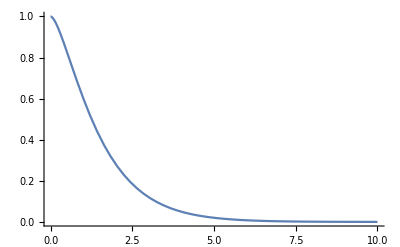

```mathematica
(* Ok this is the analogous of what I find in IHQCD *)
Plot[x BesselK[1,x],{x,0,10},PlotRange->All]
```

```mathematica
FNNAdS[k_,n_,λ_]:=FNNAdS[k,n,λ]=Exp[ⅈ sProd[k,X]]{ dfNNAdS[z]{0,Subscript[n[[λ]], 1],Subscript[n[[λ]], 2],Subscript[n[[λ]], 3],Subscript[n[[λ]], 4]},{- dfNNAdS[z] Subscript[n[[λ]], 1],0,ⅈ fNNAdS[z](Subscript[k, 1] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 1]),ⅈ fNNAdS[z](Subscript[k, 1] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 1]),ⅈ fNNAdS[z](Subscript[k, 1] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 1])},{-dfNNAdS[Q,z] Subscript[n[[λ]], 2],ⅈ fNNAdS[z](Subscript[k, 2] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 2]),0,ⅈ fNNAdS[z](Subscript[k, 2] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 2]),ⅈ fNNAdS[z](Subscript[k, 2] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 2])},{- dfNNAdS[Q,z] Subscript[n[[λ]], 3],ⅈ fNNAdS[z](Subscript[k, 3] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 3]),ⅈ fNNAdS[z](Subscript[k, 3] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 3]),0,ⅈ fNNAdS[z](Subscript[k, 3] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 3])},{- dfNNAdS[Q,z] Subscript[n[[λ]], 4],ⅈ fNNAdS[z](Subscript[k, 4] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 4]),ⅈ fNNAdS[z](Subscript[k, 4] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 4]),ⅈ fNNAdS[z](Subscript[k, 4] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 4]),0}}
```

Computing F_ab g^bc F_cd h^ad

```mathematica
(* Double vector Meson production Upper part of the diagram*)
Print["DVMP - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,3)h[a,d]
```

```mathematica
(* Double vector Meson production lower part of the diagram*)
Print["DVMP - lower part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,3)h[a,d]
```

```mathematica
(* Photon scattering Upper part of the diagram*)
Print["Photon scattering - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,3)h[a,d]
```

```mathematica
(* Photon scattering lower part of the diagram*)
Print["Photon scattering - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,3)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,1)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,2)h[a,d]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,3)h[a,d]
```